```mathematica
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};
f0=(##[[1]]^2+##[[2]]^2-2*##[[3]]^2)&;
f1=f0[##-e1]&;
f2=f0[##-e2]&;
ffund0 = (##[[1]]^2+##[[2]]^2+##[[3]]^2)^(-1/2)&;
ffund1 = ffund0[##-e1]&;
u1=Grad[f0[x,y,z],{x,y,z}]/.{x->##[[1]],y->##[[2]],z->##[[3]]} &;
(*u2= Table[ffund[##],3] &;*)
u3=Grad[ffund0[x,y,z],{x,y,z}]/.{x->##[[1]],y->##[[2]],z->##[[3]]} &;
(*u4 = Table[f[##],3] &;*)
u5 = Cross[Cross[Grad[ffund0[{x,y,z}],{x,y,z}],Grad[f1[{x,y,z}],{x,y,z}]],Grad[f2[{x,y,z}],{x,y,z}]]/.{x->##[[1]],y->##[[2]],z->##[[3]]} &;
(*u6=Curl[{ffund[x,y,z],ffund[x,y,z],f[x,y,z]},{x,y,z}]/.{x->#1,y->#2,z->#3} &;*)
expr=u5[{x,y,z}]
a=2;
```

{-(4 y)/((x^2+y^2+z^2)^(3/2))+(4 y^2)/((x^2+y^2+z^2)^(3/2))-(8 z^2)/((x^2+y^2+z^2)^(3/2))+(24 x z^2)/((x^2+y^2+z^2)^(3/2)),-(4 x y)/((x^2+y^2+z^2)^(3/2))+(24 y z^2)/((x^2+y^2+z^2)^(3/2)),-(4 x z)/((x^2+y^2+z^2)^(3/2))+(12 x^2 z)/((x^2+y^2+z^2)^(3/2))-(12 y z)/((x^2+y^2+z^2)^(3/2))+(12 y^2 z)/((x^2+y^2+z^2)^(3/2))}

```mathematica
VectorPlot3D[expr,{x,-a,a},{y,-a,a},{z,-a,a}]
```

-Graphics3D-

```mathematica
StreamPlot3D[expr,{x,-a,a},{y,-a,a},{z,-a,a},StreamPoints->Fine]
```

-Graphics3D-

```mathematica
StreamPlot3D[expr,{x,-a,a},{y,-a,a},{z,-a,a},StreamPoints->Fine]
```

-Graphics3D-

```mathematica
f1=##[[1]]^2+##[[2]]^2-##[[3]]^2&;
ContourPlot3D[f1[{x,y,z}],{x,y,z}∈Ball[{0,0,0},1],Contours->{-0.3,0,0.3},ContourStyle->Opacity[0.8],Mesh->None,RegionBoundaryStyle->None,PlotTheme->"Web"]
```

-Graphics3D-

```mathematica
(* find harmonic vector fields*)
```

```mathematica
Remove["Global`*"]
d=3; (*dimension*)
m=3; (*degree*)
Multiind={};

For[i1=0,i1<=m,i1++,
For[i2=0,i2<=m-i1,i2++,For[i3=0,i3<=m-i2-i1,i3++,Multiind= Union[Multiind,{{i1,i2,i3}}]
]
]
]
Multiind;
alpha = Subscript[a, ##]&;
multiPower=Product[(#1[[i]])^(#2[[i]]),{i,1,d}] &;
poly = Sum[alpha@@ind*multiPower[##,ind],{ind,Multiind}]&;
alphas=Table[alpha@@ind,{ind,Multiind}];

equationSystem={Laplacian[poly[{x,y,z}],{x,y,z}]};

e1={1,0,0};
criticalPointEqns[x0_]:=Module[{eqn,cp=x0},
eqn = Evaluate[Table[D[poly[{x,y,z}],var],{var,{x,y,z}}]/.{x->cp[[1]],y->cp[[2]],z->cp[[3]]}];eqn]

equationSystem = Union[criticalPointEqns[e1],criticalPointEqns[0*e1],equationSystem]

coeffEqns={};
Do[coeffEqns = Union[Union@@Union@@CoefficientList[equation,{x,y,z},Table[m,d]],coeffEqns],
{equation,equationSystem}]
For[i=1,i<=Length[coeffEqns],i++,
	coeffEqns[[i]]=coeffEqns[[i]]==0]

soln = Solve[coeffEqns][[1]];

makeNbrFree[list_]:=Select[list,!NumericQ[#]&];
(*Eliminate free variables*)
freeVars =Union[Select[alphas,!FreeQ[soln[[All,2]],#]&],Complement[alphas,soln[[All,1]]]]
freeVars1 := freeVars[[10]];
MapThread[Set,{makeNbrFree[alphas],makeNbrFree[alphas]/.{freeVars[[10]]->1,freeVars[[4]]->1}}];
MapThread[Set,{makeNbrFree[alphas],makeNbrFree[alphas]/.(##->0& /@ makeNbrFree[freeVars])}];
(*MapThread[Set,{alphas,alphas/.(##->1& /@ freeVars)}];*)
(*This part has 2 bugs: the cp-condition is not met, it behaves oddly*)
soln = Solve[coeffEqns][[1]];

(*Map solution to alphas*)
MapThread[Set,{makeNbrFree[alphas],makeNbrFree[alphas]/. soln}];
poly[{x,y,z}]
regionFunc = ##[[1]]^2+##[[2]]^2+##[[3]]^2&;
(*k=0;*)
f1=poly[{x,y,z}]/.{x->##[[1]],y->##[[2]],z->##[[3]]}&;
u1 = Grad[poly[{x,y,z}],{x,y,z}]/.{x->##[[1]],y->##[[2]],z->##[[3]]}&;
```

{a_(0,0,1),a_(0,1,0),a_(1,0,0),a_(0,0,1)+a_(1,0,1)+a_(2,0,1),a_(0,1,0)+a_(1,1,0)+a_(2,1,0),a_(1,0,0)+2 a_(2,0,0)+3 a_(3,0,0),2 a_(0,0,2)+6 z a_(0,0,3)+2 y a_(0,1,2)+2 a_(0,2,0)+2 z a_(0,2,1)+6 y a_(0,3,0)+2 x a_(1,0,2)+2 x a_(1,2,0)+2 a_(2,0,0)+2 z a_(2,0,1)+2 y a_(2,1,0)+6 x a_(3,0,0)}

{a_(0,0,0),a_(0,0,2),a_(0,0,3),a_(0,1,1),a_(0,1,2),a_(0,2,1),a_(0,3,0),a_(1,0,2),a_(1,1,1),a_(1,2,0)}

x^2/2-x^3/3-y^2/2+x y^2+y z

```mathematica
getBoundaryFunc[psi_,u_]=({D[psi[{dx,dy,dz}],dx],D[psi[{dx,dy,dz}],dy],D[psi[{dx,dy,dz}],dz]}/.{dx:>##[[1]],dy:>##[[2]],dz:>##[[3]]}).u[##]&;
Options[plotRegionStream3D]={intervalOpt->{-1,1},aOpt->2,noInflowOpt->False,levelFunction->None,plotDomain->None,plotCriticalPoints->True,streamPlotOpt->True,vectorPlotOpt->False,plotLevelOpt->True};
plotRegionStream3D[u_,psi_,OptionsPattern[]]:=With[{interval=OptionValue[intervalOpt],
a=OptionValue[aOpt],
noInflow=OptionValue[noInflowOpt],
f=OptionValue[levelFunction],
plotCriticalPoints=OptionValue[plotCriticalPoints],
streamPlot=OptionValue[streamPlotOpt],
vectorPlot=OptionValue[vectorPlotOpt],
plotLevelSets=OptionValue[plotLevelOpt]},(
(*Define the plotting region*)
plotRegion=OptionValue[plotDomain];
If[plotRegion===None,
plotRegion=ImplicitRegion[-a<x<a&&-a<y<a&&-a<z<a&&interval[[1]]<=psi[{x,y,z}]<=interval[[2]],{x,y,z}],];

plts={};
(*Plot the streamplot*)
If[streamPlot,
AppendTo[plts,StreamPlot3D[u[{x,y,z}],{x,y,z}∈plotRegion, StreamPoints->Fine,
RegionBoundaryStyle->None,StreamColorFunction->"GrayTones",PerformanceGoal->"Quality"]],];
If[vectorPlot,
AppendTo[plts,VectorPlot3D[u[{x,y,z}],{x,y,z}∈plotRegion, VectorPoints->50,
RegionBoundaryStyle->None,VectorColorFunction->"GrayTones",PerformanceGoal->"Quality"(*,StreamScale->{Tiny,All}*)]],];

(*plot boundaries*)
boundaryFunc =getBoundaryFunc[psi,u];
sigmaRegions=Table[ImplicitRegion[-a<x<a&&-a<y<a&&-a<z<a&&symb[boundaryFunc[{x,y,z}]],{x,y,z}],{symb,{LessThan[0],GreaterThan[0]}}];
If[noInflow,
AppendTo[plts,Table[ContourPlot3D[psi[{x,y,z}]==level,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->{Black,Opacity[0.3]},RegionBoundaryStyle->None,Mesh->None],
{level,interval}]];,
AppendTo[plts,Table[Table[ContourPlot3D[psi[{x,y,z}]==level,{x,y,z}∈params[[1]],ContourStyle->{params[[2]],Opacity[0.3]},RegionBoundaryStyle->None,Mesh->None],{params,{{sigmaRegions[[1]],Blue},{sigmaRegions[[2]],Red}}}],
{level,interval}]]];

(*plot critical points*)
If[plotCriticalPoints,
zeros=(NSolve[u[{x,y,z}]==0&&{x,y,z}∈plotRegion,{x,y,z},Reals])[[All,All,2]];
AppendTo[plts,ListPointPlot3D[zeros,PlotStyle->{Black,PointSize[0.04]}]];
(*plot contours*)
If[plotLevelSets,
AppendTo[plts,ContourPlot3D[f[{x,y,z}],{x,y,z}∈plotRegion,Contours->f@Transpose[zeros],ContourStyle->{Gray,Opacity[0.7]},Mesh->None,RegionBoundaryStyle->None,PlotTheme->"Web"]],],];

p=Show[plts,ImageSize->Large];
p=Legended[p,Placed[SwatchLegend[{Red,Black, Blue, Gray},{"Σ^+","Σ^0","Σ^-","level set"}],After]];
p=Legended[p,Placed[PointLegend[{Black},{"critical point"}],After]]
);
p
]
plotRegionStream3D[u1,regionFunc,levelFunction->f1,intervalOpt->{-1,20},aOpt->12, plotLevelOpt->False]
```

-Graphics3D-

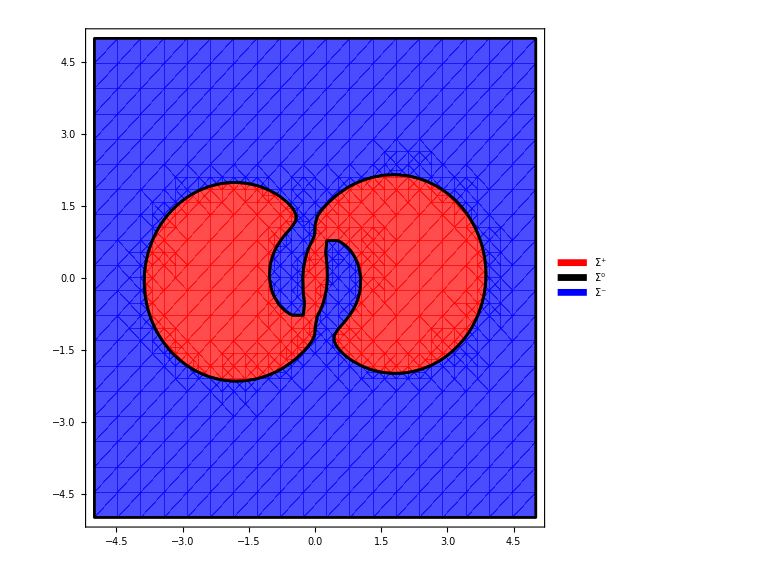

```mathematica
inverseStereographicProjection =With[{s2=Norm[##]^2},1/(s2+1)*Join[{s2-1},2*##]]&;
plotBallSurface[u_,psi_]:=With[{
a=5,
r=10},(
expr=(getBoundaryFunc[psi,u])[r*inverseStereographicProjection[{x,y}]];
plts=Table[RegionPlot[params[[1]][expr],{x,-a,a},{y,-a,a},PlotStyle->{params[[2]],Opacity[0.7]},BoundaryStyle->Black,PerformanceGoal->"Quality"],{params,{{LessThan[0],Blue},{GreaterThan[0],Red}}}];
p=Show[plts,ImageSize->Large];
p=Legended[p,Placed[SwatchLegend[{Red,Black, Blue},{"Σ^+","Σ^0","Σ^-"}],After]]
)];
plotBallSurface[u1,regionFunc]

(*sigmaRegions=Table[ImplicitRegion[-a<x<a&&-a<y<a&&symb[Evaluate[boundaryFunc[{x,y}]]],{x,y}],{symb,{LessThan[0],GreaterThan[0]}}];*)
```

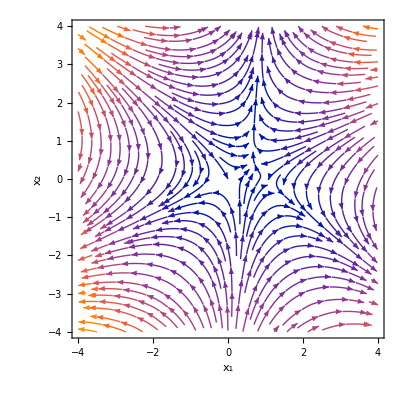

```mathematica
a=4;
StreamPlot3D[Grad[poly[{x,y,z}],{x,y,z}],{x,y,z}∈Ball[0*e1,2],RegionBoundaryStyle->None,StreamPoints->Fine]
StreamPlot[{2 x-2 x^2+4 y-8 x y+y^2,4 x-4 x^2-4 y+2 x y+3 y^2},{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

```mathematica
VectorPlot3D[Evaluate[Grad[poly[{x,y,z}],{x,y,z}]],{x,y,z}∈Ball[0*e1,2],RegionBoundaryStyle->None,VectorPoints->Fine]
```

-Graphics3D-